Delta+Kernel

```mathematica
Clear[γ,ω0,τP]
```

```mathematica
f[t_]= DiracDelta[t]/2+Exp[-Abs[t]/τP]/(2τP);
```

```mathematica
g1[t_]=InverseLaplaceTransform[(γ LaplaceTransform[f[t],t,s]x0)/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

1/(2 √(γ^2+τP^2 ω0^4))x0 (-ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2-ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))

```mathematica
g2[t_]=InverseLaplaceTransform[1/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

1/(γ √(γ^2+τP^2 ω0^4))(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2-ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))

```mathematica
(* First square *)

f1[t_]=g1[t]^2;
```

```mathematica
Limit[f1[t],τP->0,Direction->"FromAbove"]
```

ConditionalExpression[Piecewise[{{ⅇ^(-(2 t ω0^2)/γ) x0^2, γ≥0}, {0, True}}], ]

```mathematica
(* Second squared *)

2Integrate[g2[t-u]g2[t-v]2γ kB T (Exp[-(u-v)/τP]/(2τP)),{u,0,t},{v,0,u}]
```

-1/(2 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))ⅇ^(-(2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) kB T γ ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2+(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) γ √(γ^2+τP^2 ω0^4)+τP ω0^2 (-((1-4 ⅇ^((2 t √(γ^2+τP^2 ω0^4))/(γ τP))+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))+2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2)+(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)))

```mathematica
f2[t_]=-1/(2 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))ⅇ^(-(2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) kB T γ ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2+(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) γ √(γ^2+τP^2 ω0^4)+τP ω0^2 (-((1-4 ⅇ^((2 t √(γ^2+τP^2 ω0^4))/(γ τP))+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))+2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2)+(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)));
```

```mathematica
Limit[f2[t],τP->0,Direction->"FromAbove"]
```

ConditionalExpression[Piecewise[{{(2 kB T)/ω0^2, γ<0}, {(2 (1-ⅇ^(-(2 t ω0^2)/γ)) kB T)/ω0^2, True}}], (1/γ|γ|ω0^2|ω0^4|kB|T|1/ω0^2)∈ℝ&&t>0]

```mathematica
Assuming[t>=0,2Integrate[g2[t-u]g2[t-v]2γ kB T DiracDelta[u-v]/2,{u,0,t},{v,0,u}]]/.HeavisideTheta[0]->1/2
```

-1/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))ⅇ^(-(2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) kB T ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^3+γ^2 (4 ⅇ^((2 t √(γ^2+τP^2 ω0^4))/(γ τP)) τP ω0^2-4 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) τP ω0^2-√(γ^2+τP^2 ω0^4)+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP)) √(γ^2+τP^2 ω0^4))+γ τP ω0^2 ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2-(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))+2 τP^2 ω0^4 ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2-(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)))

```mathematica
f3[t_]=-1/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))ⅇ^(-(2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) kB T ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^3+γ^2 (4 ⅇ^((2 t √(γ^2+τP^2 ω0^4))/(γ τP)) τP ω0^2-4 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) τP ω0^2-√(γ^2+τP^2 ω0^4)+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP)) √(γ^2+τP^2 ω0^4))+γ τP ω0^2 ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2-(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))+2 τP^2 ω0^4 ((1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 t (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) τP ω0^2-(-1+ⅇ^((4 t √(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)));
```

```mathematica
Aux[t_]=Expand[Simplify[1/(4 kB T)(f1[t]+f2[t])(f1[0]+f2[0])]];
Aux2[t_]=Simplify[Aux[t]/.{x0^4->3((kB T)/ω0^2)^2,x0^2->(kB T)/ω0^2}];
```

```mathematica
Expand[Simplify[Assuming[{ω0>0,γ>0,kB>0,T>0,t>0},Limit[Aux2[t],τP->0,Direction->"FromAbove"]]]]
```

(kB T)/(4 ω0^4)+(ⅇ^(-(2 t ω0^2)/γ) kB T)/(2 ω0^4)

```mathematica
Cte=Assuming[{ω0>0,γ>0,kB>0,T>0,τP>0},Limit[Aux2[t],t->Infinity]];
```

```mathematica
Psi[t_]=Expand[Together[Aux2[Abs[t]]-Cte]];
```

```mathematica
Psi[t_]=FullSimplify[Together[Aux2[t]-Cte]]
```

(ⅇ^(-2 t (1/τP+ω0^2/γ)) kB T (γ τP ω0^2 (3 γ+τP ω0^2) √(γ^2+τP^2 ω0^4)+√(γ^2+τP^2 ω0^4) (2 γ^3+γ τP^2 ω0^4+3 τP^3 ω0^6) Cosh[(2 t √(γ^2+τP^2 ω0^4))/(γ τP)]+(2 γ-3 τP ω0^2) (γ+τP ω0^2) (γ^2+τP^2 ω0^4) Sinh[(2 t √(γ^2+τP^2 ω0^4))/(γ τP)]))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))

```mathematica
Together[(γ τP ω0^2 (3 γ+τP ω0^2) √(γ^2+τP^2 ω0^4))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))]
```

(γ τP (3 γ+τP ω0^2))/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))

```mathematica
Assuming[{ω0>0,γ>0,kB>0,T>0,τP>0},Limit[Psi[t],t->Infinity]]
```

0

```mathematica
Together[Assuming[{ω0>0,γ>0,kB>0,T>0,τP>0},FourierTransform[Psi[t],t,ω]]]
```

(kB √(2/π) T γ (64 γ^2+46 γ^2 τP^2 ω^2+3 γ^2 τP^4 ω^4+80 γ τP ω0^2+30 γ τP^3 ω^2 ω0^2+48 τP^2 ω0^4+12 τP^4 ω^2 ω0^4))/(ω0^2 (64 γ^4 ω^2+20 γ^4 τP^2 ω^4+γ^4 τP^4 ω^6+192 γ^3 τP ω^2 ω0^2+24 γ^3 τP^3 ω^4 ω0^2+256 γ^2 ω0^4+320 γ^2 τP^2 ω^2 ω0^4+20 γ^2 τP^4 ω^4 ω0^4+512 γ τP ω0^6+192 γ τP^3 ω^2 ω0^6+256 τP^2 ω0^8+64 τP^4 ω^2 ω0^8))

```mathematica
Together[Psi[0]-kB T/(2 ω0^4)]
```

(kB T τP)/(4 ω0^2 (γ+τP ω0^2))

```mathematica
Assuming[{γ>0,ω0>0,τP>0},Integrate[Psi[t]/Psi[0],{t,0,Infinity}]]
```

(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))

```mathematica
Series[(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)),{τP,0,1}]
```

γ/(2 ω0^2)-(5 τP)/8+O[τP]^2

```mathematica
τR2=τR+Together[(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))-γ/(2 ω0^2)]
```

τR-(γ (5 γ τP+3 τP^2 ω0^2))/(4 (γ+τP ω0^2) (2 γ+3 τP ω0^2))

```mathematica
τR2=Together[(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))-(γ ((kB T)/(2 ω0^4)))/(2 ω0^2 Psi[0])]
```

-(γ (3 γ τP+τP^2 ω0^2))/(4 (γ+τP ω0^2) (2 γ+3 τP ω0^2))

2 Deltas

```mathematica
f[t_]=DiracDelta[t];
```

```mathematica
InverseLaplaceTransform[(γ LaplaceTransform[f[t],t,s]x0)/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

ⅇ^(-(t ω0^2)/γ) x0

```mathematica
Assuming[t>=0,InverseLaplaceTransform[1/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]]
```

(ⅇ^(-(t ω0^2)/γ))/γ

```mathematica
f1[t_]=(ⅇ^(-(t ω0^2)/γ) x0)^2;
```

```mathematica
Assuming[t>0,Integrate[((ⅇ^(-((t-u) ω0^2)/γ))/γ)((ⅇ^(-((t-v) ω0^2)/γ))/γ)2γ kB T DiracDelta[u-v],{u,0,t},{v,0,t}]]
```

((1-ⅇ^(-(2 t ω0^2)/γ)) kB T)/ω0^2

```mathematica
Assuming[t>0,Integrate[((ⅇ^(-((t-u) ω0^2)/(2 γ)))/(2 γ))^2 4γ kB T ,{u,0,t}]]
```

((1-ⅇ^(-(t ω0^2)/γ)) kB T)/ω0^2

```mathematica
f2[t_]=((1-ⅇ^(-(t 2 ω0^2)/γ)) kB T)/ω0^2;
```

```mathematica
Aux[t_]=Expand[Simplify[1/(4 kB T)(f1[t]+f2[t])(f1[0]+f2[0])]]
```

(ⅇ^(-(2 t ω0^2)/γ) x0^4)/(4 kB T)+x0^2/(4 ω0^2)-(ⅇ^(-(2 t ω0^2)/γ) x0^2)/(4 ω0^2)

```mathematica
Aux2[t_]=Aux[t]/.{x0^4->3((kB T)/ω0^2)^2,x0^2->(kB T)/ω0^2}
```

(kB T)/(4 ω0^4)+(ⅇ^(-(2 t ω0^2)/γ) kB T)/(2 ω0^4)

```mathematica
Limit[Aux2[t],t->Infinity]
```

ConditionalExpression[(kB T)/(4 ω0^4), (kB T|kB|T)∈ℝ&&γ ω0^2>0]

```mathematica
Cte=(kB T)/(4 ω0^4);
```

```mathematica
Psi[t_]=FullSimplify[Aux2[t]-Cte]
```

(ⅇ^(-(2 t ω0^2)/γ) kB T)/(2 ω0^4)

```mathematica
FourierTransform[Exp[-ω1 Abs[ t]],t,ω]
```

(√(2/π) ω1)/(ω^2+ω1^2)

```mathematica
(FourierTransform[Exp[-Abs[t]/τ]/τ/2,t,s]/.s->0)-FourierTransform[DiracDelta[t],t,s]
```

0

OPtimal protocols

```mathematica
Aux3[t_]=(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^4)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^4)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 τP)/(8 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 τP)/(8 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^3 ω0^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^3 ω0^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^4 ω0^4)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^4 ω0^4)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2)/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP)/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4));
Psi[t_]=Aux3[t]/Aux3[0];
```

```mathematica
dPsi[t_]=D[Aux3[t]/Aux3[0],t]/. Abs'[t]->Sign[t]
```

(-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(2 τP ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^2 ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(2 τP ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^2 ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(4 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((2 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP ((2 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^4 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 τP ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^3 ω0^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^4 ω0^4 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)))/((kB T γ τP^2)/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(kB T γ^3)/(2 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 kB T γ^2 τP)/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 kB T τP^3 ω0^2)/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)))

```mathematica
ddPsi[t_]=D[dPsi[t],t]/. {Abs'[t]->Sign[t],Sign'[t]->2DiracDelta[t]}
```

(-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(τP ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^2 ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(τP ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^2 ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(2 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((4 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP ((4 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP^2 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^4 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 τP ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^3 ω0^2 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^4 ω0^4 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^2 ((8 √(γ^2+τP^2 ω0^4) DiracDelta[t])/(γ τP)-(4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) DiracDelta[t])/(γ τP)))/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(τP^2 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 τP ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^2 ω0^4 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 γ^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 γ (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(τP^2 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^(-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP ω0^2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))^2 Sign[t]^2)/(2 γ^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((2 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((2 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP ((2 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^2 τP^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^4 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 τP ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^3 ω0^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))-(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^4 ω0^4 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ τP^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T γ^3 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 ⅇ^((4 √(γ^2+τP^2 ω0^4) Abs[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Abs[t])/(γ τP)) kB T τP^3 ω0^2 ((4 √(γ^2+τP^2 ω0^4) Sign[t])/(γ τP)-(2 (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)) Sign[t])/(γ τP))^2)/(8 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)))/((kB T γ τP^2)/(2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(kB T γ^3)/(2 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 kB T γ^2 τP)/(4 ω0^2 (γ+τP ω0^2) (γ^2+τP^2 ω0^4))+(3 kB T τP^3 ω0^2)/(4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)))

```mathematica
Integrate[ddPsi[t]Exp[-s t],{t,0,Infinity}]/.HeavisideTheta[0]->1/2
```

ConditionalExpression[(4 ω0^2 (γ+τP ω0^2) (-3 s^3 γ^2 τP^2+s^2 γ τP (-13 γ-6 τP ω0^2)+4 s (-2 γ^2-3 γ τP ω0^2)))/(γ (γ (2+s τP)+2 τP ω0^2) (2 γ+3 τP ω0^2) (s γ (4+s τP)+4 (2+s τP) ω0^2)), ]

```mathematica
-Series[1/(s ((4 ω0^2 (γ+τP ω0^2) (-3 s^3 γ^2 τP^2+s^2 γ τP (-13 γ-6 τP ω0^2)+4 s (-2 γ^2-3 γ τP ω0^2)))/(γ (γ (2+s τP)+2 τP ω0^2) (2 γ+3 τP ω0^2) (s γ (4+s τP)+4 (2+s τP) ω0^2)))),{s,0,3}]
```

1/s^2+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) s)-(γ^2 (28 γ^2 τP+17 γ τP^2 ω0^2+3 τP^3 ω0^4))/(16 (ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)^2))+(γ^2 (300 γ^3 τP^2+269 γ^2 τP^3 ω0^2+105 γ τP^4 ω0^4+18 τP^5 ω0^6) s)/(64 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)^3)-((γ^2 (3228 γ^4 τP^3+3881 γ^3 τP^4 ω0^2+2295 γ^2 τP^5 ω0^4+756 γ τP^6 ω0^6+108 τP^7 ω0^8)) s^2)/(256 (ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)^4))+(γ^2 (34764 γ^5 τP^4+52565 γ^4 τP^5 ω0^2+40917 γ^3 τP^6 ω0^4+19386 γ^2 τP^7 ω0^6+5292 γ τP^8 ω0^8+648 τP^9 ω0^10) s^3)/(1024 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)^5)+O[s]^4

Optimal protocol

```mathematica
Psi[t_]=(ⅇ^(-2 t (1/τP+ω0^2/γ)) kB T (γ τP ω0^2 (3 γ+τP ω0^2) √(γ^2+τP^2 ω0^4)+√(γ^2+τP^2 ω0^4) (2 γ^3+γ τP^2 ω0^4+3 τP^3 ω0^6) Cosh[(2 t √(γ^2+τP^2 ω0^4))/(γ τP)]+(2 γ-3 τP ω0^2) (γ+τP ω0^2) (γ^2+τP^2 ω0^4) Sinh[(2 t √(γ^2+τP^2 ω0^4))/(γ τP)]))/(4 ω0^4 (γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2));
p[t_]=1/τ;
popt[t_]=1/(τ+2((γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))))+2((γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))/(τ+2((γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))))(DiracDelta[t]+DiracDelta[τ-t]);
```

```mathematica
Aux5[τ_]=Assuming[{γ>0,ω0>0,τP>0},Integrate[Psi[t-u],{t,0,τ},{u,0,t}]];
```

```mathematica
Expand[popt[t]popt[u]];
```

```mathematica
Aux6[τ_]=Aux5[τ]/(τ+2((γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))))^2;
```

```mathematica
Aux7[τ_]=Assuming[{γ>0,ω0>0,τP>0,τ>0,t>=0,u>=0},Integrate[Psi[t-u]((5 γ^2 τP DiracDelta[t])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(2 γ^3 DiracDelta[t])/(ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(3 γ τP^2 ω0^2 DiracDelta[t])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(5 γ^2 τP DiracDelta[u])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(2 γ^3 DiracDelta[u])/(ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(3 γ τP^2 ω0^2 DiracDelta[u])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2))+(5 γ^2 τP DiracDelta[-t+τ])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(2 γ^3 DiracDelta[-t+τ])/(ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(3 γ τP^2 ω0^2 DiracDelta[-t+τ])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(5 γ^2 τP DiracDelta[-u+τ])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(2 γ^3 DiracDelta[-u+τ])/(ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2)+(3 γ τP^2 ω0^2 DiracDelta[-u+τ])/(2 (γ+τP ω0^2) (2 γ+3 τP ω0^2) (τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(2 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2)))^2),{t,0,τ},{u,0,t}]]/.HeavisideTheta[0]->1/2;
```

```mathematica
Simplify[Aux5[τ]/τ^2];
Simplify[Aux6[τ]+Aux7[τ]];
```

```mathematica
Wirr[τ]=1/(128 τ^2 ω0^8)γ ((8 (-1+ⅇ^(-(2 τ (γ+τP ω0^2))/(γ τP))) γ^2 τP^3 ω0^6 (3 γ+τP ω0^2))/((γ+τP ω0^2)^3 (γ^2+τP^2 ω0^4))+(16 γ τ τP^2 ω0^6 (3 γ+τP ω0^2))/((γ+τP ω0^2)^2 (γ^2+τP^2 ω0^4))+(8 τ ω0^2 (4 γ^2-3 γ τP ω0^2+3 τP^2 ω0^4))/(γ^2+τP^2 ω0^4)+1/(√(γ^2+τP^2 ω0^4))ⅇ^(-(2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) (4 γ-3 τP ω0^2) ((-1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))) γ+(-1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+(1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) √(γ^2+τP^2 ω0^4))-(2 γ τP ω0^2 (4 γ^2-3 γ τP ω0^2+3 τP^2 ω0^4) (-(-1+ⅇ^(-(2 τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP)))/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))-(-1+ⅇ^(-(2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)))/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))/(γ^2+τP^2 ω0^4));
Wirropt[τ]=1/(128 ω0^8)γ (1/((τ+(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 γ^2 ω0^2+10 γ τP ω0^4+6 τP^2 ω0^6))^2)((8 (-1+ⅇ^(-(2 τ (γ+τP ω0^2))/(γ τP))) γ^2 τP^3 ω0^6 (3 γ+τP ω0^2))/((γ+τP ω0^2)^3 (γ^2+τP^2 ω0^4))+(16 γ τ τP^2 ω0^6 (3 γ+τP ω0^2))/((γ+τP ω0^2)^2 (γ^2+τP^2 ω0^4))+(8 τ ω0^2 (4 γ^2-3 γ τP ω0^2+3 τP^2 ω0^4))/(γ^2+τP^2 ω0^4)+1/(√(γ^2+τP^2 ω0^4))ⅇ^(-(2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)) (4 γ-3 τP ω0^2) ((-1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))) γ+(-1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+(1+ⅇ^((4 τ √(γ^2+τP^2 ω0^4))/(γ τP))-2 ⅇ^((2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) √(γ^2+τP^2 ω0^4))-(2 γ τP ω0^2 (4 γ^2-3 γ τP ω0^2+3 τP^2 ω0^4) (-(-1+ⅇ^(-(2 τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP)))/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))-(-1+ⅇ^(-(2 τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP)))/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))/(γ^2+τP^2 ω0^4))-(8 ⅇ^(-(2 τ (γ+τP ω0^2))/(γ τP)) γ ω0^6 (2 γ+3 τP ω0^2) (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4) (√(γ^2+τP^2 ω0^4) (2 γ τP^2 ω0^4 (3 γ+τP ω0^2)-ⅇ^(2 τ (1/τP+ω0^2/γ)) (4 γ^4+5 γ^3 τP ω0^2+7 γ^2 τP^2 ω0^4+5 γ τP^3 ω0^6+3 τP^4 ω0^8))+(γ+τP ω0^2)^2 √(γ^2+τP^2 ω0^4) (4 γ^2-3 γ τP ω0^2+3 τP^2 ω0^4) Cosh[(2 τ √(γ^2+τP^2 ω0^4))/(γ τP)]+(γ+τP ω0^2)^2 (4 γ^3-3 γ^2 τP ω0^2+4 γ τP^2 ω0^4-3 τP^3 ω0^6) Sinh[(2 τ √(γ^2+τP^2 ω0^4))/(γ τP)]))/((γ+τP ω0^2) (γ^2+τP^2 ω0^4)^(3/2) (4 γ^3 ω0+γ^2 (4 τ+5 τP) ω0^3+γ τP (10 τ+3 τP) ω0^5+6 τ τP^2 ω0^7)^2));
```

```mathematica
γ=2;
ω0=1;
τP=1;
kB=1;
T=1;

(γ (4 γ^2+5 γ τP ω0^2+3 τP^2 ω0^4))/(4 ω0^2 (γ+τP ω0^2) (2 γ+3 τP ω0^2))
```

29/42

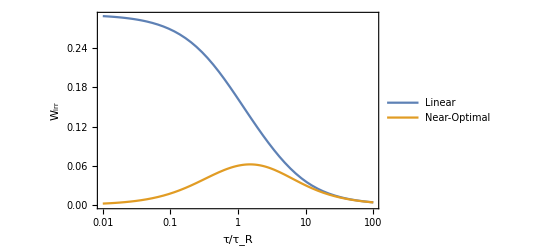

```mathematica
LogLinearPlot[{Wirr[τ],Wirropt[τ]},{τ,0.01,100},Frame->True, FrameLabel->{"τ/τ_R","W_irr"},FrameStyle->Directive[Bold,Black,12],PlotLegends->Placed[{"Linear","Near-Optimal"},{Scaled[0.8],Scaled[0.8]}]]

Clear[γ,ω0,τP,kB,T]
```